```mathematica
(*Harmonic Zeta Zero Predictor with Dynamic Ratio Evolution*)
ClearAll[predictZerosWithRatio]

predictZerosWithRatio[iterations_,alpha_:1.5,target_:0.5,initialRatio_:0.47]:=Module[{predictions,ratios,n,previous,ratio,correction,value},predictions={target};
ratios={initialRatio};
For[n=1,n<=iterations,n++,previous=predictions[[-1]];
ratio=ratios[[-1]]+(target-previous)*(0.035/(n+1));
correction=(target-previous)/(alpha*ratio*(n+1));
value=previous*(-1)^n*Cos[n/π]+correction+ratio*((target-previous)/(n+1));
AppendTo[predictions,value];
AppendTo[ratios,ratio];];
<|"Predictions"->predictions,"Ratios"->ratios|>]
```

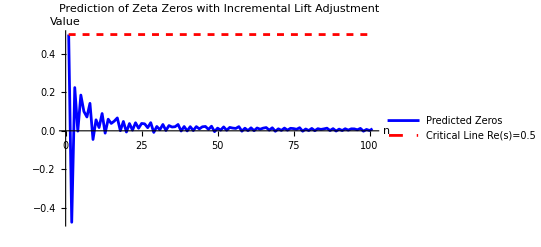

```mathematica
results=predictZerosWithRatio[100];
predicted=results["Predictions"];

ListLinePlot[{predicted,ConstantArray[0.5,Length[predicted]]},PlotStyle->{Blue,{Dashed,Red}},PlotLegends->{"Predicted Zeros","Critical Line Re(s)=0.5"},AxesLabel->{"n","Value"},PlotLabel->"Prediction of Zeta Zeros with Incremental Lift Adjustment"]
```

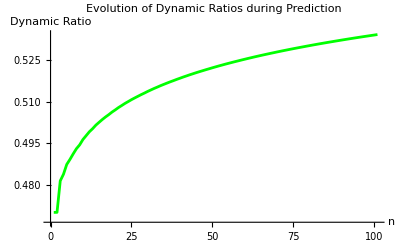

```mathematica
ListLinePlot[results["Ratios"],PlotStyle->Green,AxesLabel->{"n","Dynamic Ratio"},PlotLabel->"Evolution of Dynamic Ratios during Prediction"]
```

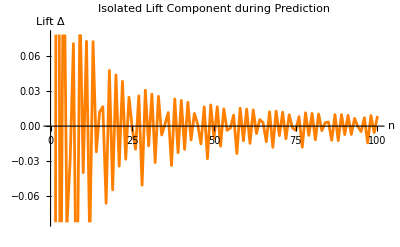

```mathematica
lift=Differences[results["Predictions"]];
ListLinePlot[lift,PlotStyle->Orange,AxesLabel->{"n","Lift Δ"},PlotLabel->"Isolated Lift Component during Prediction"]
```